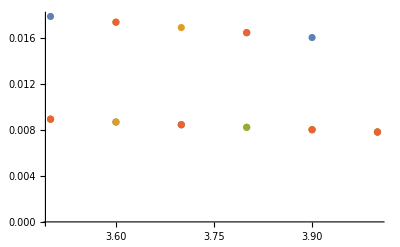

```mathematica
a11={{3.5,91/(3.5×32)}, {3.6,95/(3.6×32)},{3.7,98/(3.7×32)},{3.8,101/(3.8×32)}, {3.9,104/(3.9×32)},{4.0,109/(4×32)}};
a21={{3.5,88/(3.5×32)}, {3.6,91/(3.6×32)},{3.7,94/(3.7×32)},{3.8,98/(3.8×32)}, {3.9,101/(3.9×32)},{4.0,106/(4×32)}};
a31={{3.5,86/(3.5×32)}, {3.6,89/(3.6×32)},{3.7,93/(3.7×32)},{3.8,96/(3.8×32)}, {3.9,100/(3.9×32)},{4.0,104/(4×32)}};
a41={{3.5,85/(3.5×32)}, {3.6,88/(3.6×32)},{3.7,92/(3.7×32)},{3.8,95/(3.8×32)}, {3.9,99/(3.9×32)},{4.0,103/(4×32)}};
a12={{3.5,93/(3.5×32)}, {3.6,96/(3.6×32)},{3.7,99/(3.7×32)},{3.8,103/(3.8×32)}, {3.9,106/(3.9×32)},{4.0,110/(4×32)}};
a22={{3.5,89/(3.5×32)}, {3.6,92/(3.6×32)},{3.7,96/(3.7×32)},{3.8,99/(3.8×32)}, {3.9,102/(3.9×32)},{4.0,107/(4×32)}};
a32={{3.5,87/(3.5×32)}, {3.6,91/(3.6×32)},{3.7,94/(3.7×32)},{3.8,97/(3.8×32)}, {3.9,101/(3.9×32)},{4.0,105/(4×32)}};
a42={{3.5,86/(3.5×32)}, {3.6,90/(3.6×32)},{3.7,93/(3.7×32)},{3.8,97/(3.8×32)}, {3.9,100/(3.9×32)},{4.0,104/(4×32)}};
a1=a12-a11*Table[{0,1},{i,0,5}];
a2=a22-a21*Table[{0,1},{i,0,5}];
a3=a32-a31*Table[{0,1},{i,0,5}];
a4=a42-a41*Table[{0,1},{i,0,5}];
ListPlot[{a1,a2,a3,a4}]
```

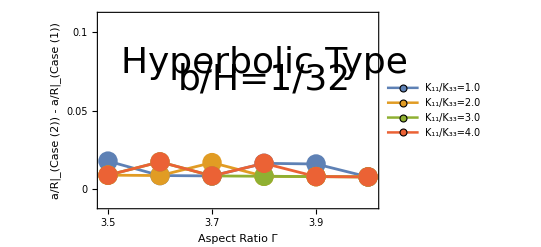

```mathematica
ListPlot[{a1,a2,a3,a4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0,0.05,0.1},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.49,4.01},{-0.01,0.11}},FrameLabel->{{"a/R|_(Case (2)) - a/R|_(Case (1))", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{3.8,0.08}],Text[Style["b/H=1/32",Directive[Black,36]],{3.8,0.07}]}]
```